## Documentation

### Atlas Raw Data Structures

JSON / JLink -Xmx : http://reference.wolfram.com/mathematica/ref/message/Import/nojmem.html

atlas documentation : https://atlas.ripe.net/docs/data_struct 
RFC4950 ICMP Extensions for Multiprotocol Label Switching : http://tools.ietf.org/html/rfc4950
paris traceroute version : http://www.paris-traceroute.net

howto/AddErrorBarsToChartsAndPlots

### Data Source

```mathematica
defaultSampleDir=FileNameJoin[{NotebookDirectory[], "data"}];
```

```mathematica
(* 80mb JSON file *)sampleJSONSrc=If[True,FileNameJoin[{defaultSampleDir,"RIPE-Atlas-measurement-digifortress-traceroute.json"}],
"https://atlas.ripe.net/api/v1/measurement/1608005/result/"];
```

```mathematica
(* 118K JSON file *)sampleJSONSrc= FileNameJoin[{defaultSampleDir,"RIPE-Atlas-measurement-72.129.45.3-traceroute.json"}];
```

#### Read JSON file

```mathematica
Needs["JLink`"];
UninstallJava[];
ReinstallJava[CommandLine->"java",JVMArguments->"-Xmx2024m"];

sampleJSON=Import[sampleJSONSrc, "JSON"];

UninstallJava[];
```

```mathematica
Dimensions[sampleJSON]
```

{26718,17}

### Transcoding

#### Map Atlas JSON Traceroute To Summary

```mathematica
unixTimeToHST[x_Integer]:=DateList[AbsoluteTime[{1970,1,1,2,0,0}]+x,TimeZone->-10];
(* TEST *)
unixTimeToHST[1399725833]
```

{2014,5,10,9,43,53.}

```mathematica
(* summarizeTestsInsideSingleHop : normalizes a single ping in the hop's interval test *)
Clear[summarizeTestsInsideSingleHop];
summarizeTestsInsideSingleHop::usage="summarizeTestsInsideSingleHop flattens out results - including optional results - into a standard format. This implies some of that optional info might well be dropped.  See normalizedResult::canonicalResult";
normalizedResult::canonicalResult="{from, rtt, size, ttl, errorsIfAny}";
(* MESSAGES *)
summarizeTestsInsideSingleHop::icmpnext="(opt) icmpnext chunk omitted";
summarizeTestsInsideSingleHop::unexpectedArg="`1`";
(* IMPLEMENTATION *) 
summarizeTestsInsideSingleHop[{"from"->from_, "rtt" ->rtt_,"size"->size_Integer, "ttl"->ttl_Integer}]:= {from,rtt, size, ttl,{}};
(* ittl (optional) TimeToLive in packet that triggered the error ICMP. Omitted if equal to 1 (int) *)
summarizeTestsInsideSingleHop[{"from"->from_, "ittl"->ittl_Integer,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= {from,rtt, size,ttl,{"ittl"->ittl}};
(* icmpext (optional)  *)
summarizeTestsInsideSingleHop[{"from"->from_, "icmpext"->icmpext_List,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= 
Block[{},
{from,rtt,size,ttl,{"icmpext"->icmpext}}];
summarizeTestsInsideSingleHop[{"from"->from_, "icmpext"->icmpext_List,"ittl"->ittl_Integer,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= 
Block[{},
{from,rtt,size,ttl,{"icmpext"->icmpext, "ittl"->ittl}}];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
summarizeTestsInsideSingleHop [x_]:= Message[summarizeTestsInsideSingleHop::unexpectedArg,x];
(* TEST *)
atlasToComputableForm[sampleJSON[[3]]]//TableForm
```

summarizeTestsInsideSingleHop::unexpectedArg: {"x" → "*"}

General::stop: Further output of summarizeTestsInsideSingleHop :: unexpectedArg will be suppressed during this calculation.

Part::partd: Part specification Null ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification Null ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification Null ⟦ 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

prb_id→1165
proto→ICMP
paris_id→1
type→traceroute
interval→{{2014,3,30,20,2,23.},{2014,3,30,20,2,41.}}
proto→ICMP
hopsAsCDF→{{192.168.1.1,{1.419,1.48367,1.562},68,64,0},{24.94.68.1,{24.414,29.831,40.547},28,254,0},{24.25.230.137,{15.078,18.3483,21.107},28,253,0},{72.129.45.68,{14.553,16.6253,19.34},68,252,0},{72.129.45.52,{20.371,21.9513,23.148},140,246,0},{72.129.45.43,{21.634,24.1,25.385},140,247,0},{72.129.45.67,{22.071,23.7473,26.648},28,249,0},{24.25.225.149,{17.563,18.9107,20.034},28,248,0},{Null⟦1⟧,{0,0,0},Null⟦3⟧,Null⟦4⟧,0},{66.192.254.82,{79.95,80.8045,81.659},28,242,0},{66.162.247.242,{78.486,79.417,80.21},28,242,0},{205.172.1.1,{77.842,84.382,92.591},40,52,0}}

```mathematica
(* summarizeHop : summarizes RTTs and errors from a specific hop in the traceroute for a probe *)
Clear[summarizeHop];
(* MESSAGES *)
summarizeHop::unexpectedArg="`1`";
(* IMPLEMENTATION *)
summarizeHop[{"hop"->hopID_, "result"->testsInsideHop_List}]:= 
Block[{DEBUGargOnly=False},
If[DEBUGargOnly,testsInsideHop,
Block[
{errorFreeTests, firstResult,erroredTests,errorFreeRTTs,from,allNormedResults, size,ttl,  errorCount },
(* Exected form returned is {from, rtt, size, ttl, markAsErrorP, "errorDetails"->{(listOfRules}|{}) } *)
allNormedResults=summarizeTestsInsideSingleHop /@ testsInsideHop;
(* classify by success or failures *)
errorFreeTests=Cases[allNormedResults,{_,_,_,_,{}}];
erroredTests=Cases[allNormedResults,{_,_,_,_,Length[_]>0}];
errorFreeTests=Cases[allNormedResults,{_,_,_,_,_}];
(* assert - the following values should always be the same during the interval test *)
(* TODO - IF TTL and SIZE do change during interval testing, is that indicitive of an error?  *)
firstResult=allNormedResults[[1]];
from=firstResult[[1]];
size=firstResult[[3]];
ttl=firstResult[[4]];
errorFreeRTTs=If[Length[errorFreeTests]>0, errorFreeTests[[All,2]],{0,0}];
(* process erroredResults *)
errorCount=Length[erroredTests];
(* returning... *)
{from, {Min[errorFreeRTTs],Mean[errorFreeRTTs], Max[errorFreeRTTs]}, size,ttl, errorCount}
]]
];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
summarizeHop[x_]:=Message[summarizeHop::unexpectedArg,x];
(* TEST *)
atlasToComputableForm[sampleJSON[[1]]]//TableForm
```

prb_id→10546
proto→ICMP
paris_id→1
type→traceroute
interval→{{2014,5,10,9,43,53.},{2014,5,10,9,43,54.}}
proto→ICMP
hopsAsCDF→{{192.168.1.1,{0.561,0.617333,0.683},68,64,0},{70.95.176.1,{23.54,27.7587,29.982},28,254,0},{24.25.230.229,{11.997,12.55,13.312},28,253,0},{72.129.45.3,{11.082,13.3547,15.036},40,252,0}}

```mathematica
(* walkProbeTraceroute : summarizes an individual probe's traceroute *)
Clear[walkProbeTraceroute];
(* MESSAGES *)
walkProbeTraceroute::usage="walkProbeTraceroute works through the results";
walkProbeTraceroute::unexpectedArg="`1`";
(* IMPLEMENTATION *)
(* Assert : hop is dropped in the expectation walkProbeTraceroute is always called in traversal order of the list of hops *)
walkProbeTraceroute[hopsInTraceroute_List]:= 
(* Summary roll-up results of entire traceroute path is applied here *)
Block[{DEBUGshowArgOnly=False},
If[DEBUGshowArgOnly,hopsInTraceroute,
summarizeHop/@ hopsInTraceroute]];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
walkProbeTraceroute[x_]:=Message[walkProbeTraceroute::unexpectedArg,x];
(* TEST *)
atlasToComputableForm[sampleJSON[[{1,5}]]]//TableForm
```

prb_id→10546 | proto→ICMP | paris_id→1 | type→traceroute | interval→{{2014,5,10,9,43,53.},{2014,5,10,9,43,54.}} | proto→ICMP | hopsAsCDF→{{192.168.1.1,{0.561,0.617333,0.683},68,64,0},{70.95.176.1,{23.54,27.7587,29.982},28,254,0},{24.25.230.229,{11.997,12.55,13.312},28,253,0},{72.129.45.3,{11.082,13.3547,15.036},40,252,0}}
prb_id→14720 | proto→ICMP | paris_id→1 | type→traceroute | interval→{{2014,5,10,9,47,6.},{2014,5,10,9,47,9.}} | proto→ICMP | hopsAsCDF→{{128.171.0.1,{0.503,0.558667,0.664},28,255,0},{128.171.213.14,{0.965,1.01733,1.055},28,253,0},{205.166.205.22,{1.021,1.038,1.07},28,253,0},{64.57.21.49,{65.542,75.0423,93.999},28,251,0},{198.32.134.83,{65.699,68.3457,73.565},28,250,0},{66.109.6.144,{93.623,94.409,95.914},140,246,0},{66.109.9.44,{93.606,94.307,95.034},140,247,0},{66.109.6.7,{93.65,94.249,95.438},68,248,0},{107.14.19.33,{93.625,95.506,99.216},68,247,0},{72.129.17.1,{93.88,96.3913,97.679},68,246,0},{72.129.17.5,{97.545,97.7683,97.991},68,245,0},{72.129.17.2,{95.389,96.877,97.699},68,246,0},{72.129.45.3,{73.531,73.7173,73.901},40,249,0}}

```mathematica
(* atlasToComputableForm : Initiates the walk of traceroute results *)
Clear[atlasToComputableForm];
atlasToComputableForm::usage="Summarizes results from all probes";

atlasToComputableForm[{af_Rule,dstAddr_Rule,dstName_Rule, endTime_Rule,from_Rule, "fw"->4610,groupID_Rule,msmID_Rule,msmName_Rule,parisID_Rule,prbID_Rule,proto_Rule,"result"->result_List,size_Rule,srcAddr_Rule,timeStamp_Rule,type_Rule}] :=
Block[{DEBUGshowResultOnly=False},
If[DEBUGshowResultOnly,walkProbeTraceroute[result],{prbID,
proto,
parisID,
type,
"interval"->{unixTimeToHST["timestamp"/.timeStamp],
unixTimeToHST["endtime"/.endTime]}, 
proto,
"hopsAsCDF"->walkProbeTraceroute[result]}
]];
(* Generalize for a list *)
atlasToComputableForm[aList_List]:= atlasToComputableForm /@ aList;
(* TEST *)
atlasToComputableForm[sampleJSON[[{3,4}]]]//TableForm
```

prb_id→12735 | proto→ICMP | paris_id→1 | type→traceroute | interval→{{2014,5,10,9,45,7.},{2014,5,10,9,45,7.}} | proto→ICMP | hopsAsCDF→{{10.0.1.1,{0.396,0.475333,0.617},28,255,0},{66.75.112.1,{16.184,20.6163,24.6},28,254,0},{24.25.231.25,{8.858,9.836,11.353},28,253,0},{72.129.45.3,{10.168,10.45,10.931},40,252,0}}
prb_id→1178 | proto→ICMP | paris_id→1 | type→traceroute | interval→{{2014,5,10,9,46,25.},{2014,5,10,9,46,26.}} | proto→ICMP | hopsAsCDF→{{24.94.68.1,{27.899,28.2573,28.45},28,255,0},{24.25.230.137,{16.311,21.7453,32.278},28,254,0},{72.129.45.68,{14.524,16.3823,18.212},68,253,0},{72.129.45.52,{17.98,18.803,20.36},68,251,0},{72.129.45.0,{68.115,68.322,68.488},68,251,0},{66.75.161.48,{68.44,69.815,70.708},68,251,0},{72.129.45.3,{66.755,69.3303,71.401},40,251,0}}

```mathematica
(* pathsOnly extracts the unique traceroute path from all tests *)
Clear[pathOnly];
pathOnly::usage="Given a JSON traceroute list, distill down to the unique set of traceroute paths";
pathOnly::unexpectedArg="`1`";
(* IMPLEMENTATION *)
pathOnly[{"prb_id"->prbID_Integer,"proto"->proto_String,"paris_id"->parisID_Integer,"type"->type_String,"interval"->interval_List, "proto"->proto_String, "hopsAsCDF"->hopsAsCDF_List}]:= {
Block[{},
Flatten[{prbID,hopsAsCDF[[All,1]]}]]
};
pathOnly[aList_List]:= Flatten[pathOnly/@ aList,1];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
pathOnly[x_]:=Message[pathOnly::unexpectedArg,x];
(* TEST *)
pathOnly[atlasToComputableForm[sampleJSON[[{3,4}]]]]//MatrixForm
```

({12735,10.0.1.1,66.75.112.1,24.25.231.25,72.129.45.3}
{1178,24.94.68.1,24.25.230.137,72.129.45.68,72.129.45.52,72.129.45.0,66.75.161.48,72.129.45.3})

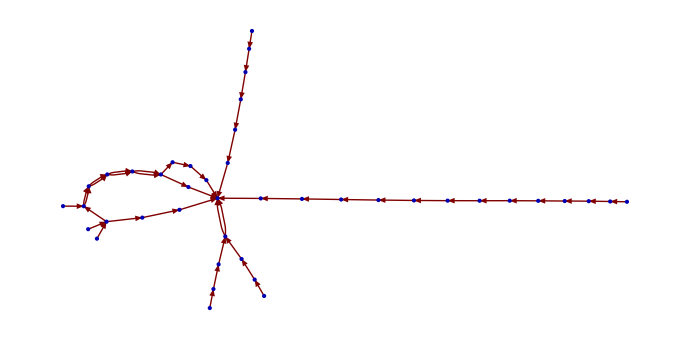

```mathematica
GraphPlot[Flatten[DeleteDuplicates[Rule[#[[1]],#[[2]]]&/@Partition[#,2,1]&/@pathOnly[atlasToComputableForm[sampleJSON]]],1], MultiedgeStyle->True, DirectedEdges->True]
```

### Scratch

#### Extracting values from nested rules in JSON data

http://mathematica.stackexchange.com/questions/3111/extracting-values-from-nested-rules-in-json-data